# Pertołów

## Dane

### Nazwy plików konfiguracyjnych

```mathematica
(*fileg="configgLG"; 
*)
```

### Tensor metryczny

```mathematica
(*{g,x}=ReadList[fileg]*)
```

```mathematica
(* kowariantny tensor metryczny gμν - NALEŻY USTAWIĆ!; uwaga! numeracja w tabeli jest od 1 *)
(* wymiar przestrzeni: namx = liczba wierszy = liczba kolumn w tensorze metrycznym *)
nmax=4; 

(* longitudinal gauge, brak przestrzennych elementów pozadiagonalnych w tensorze energii-pędu, czas kosmiczny, zerowa krzywizna *)
g = Table[Which[ n == m && n==1, -(1+2*P*Φ[t,x1,x2,x3]),n == m && n==2, a[t]^2*(1-2*P*Φ[t,x1,x2,x3]),n == m && n==3, a[t]^2*(1-2*P*Φ[t,x1,x2,x3]),n == m && n==4, a[t]^2*(1-2*P*Φ[t,x1,x2,x3]), True , 0 ], {n , nmax } , {m , nmax }];
(* tensor metryczny bez perturbacji *)
(*g = Table[Which[ n == m && n==1, -1,n == m && n==2, a[t]^2,n == m && n==3, a[t]^2,n == m && n==4, a[t]^2, True , 0 ], {n , nmax } , {m , nmax }];*)

(* czy zmienne Mukhanova-Sasakiego stosować *)
mMS=True;
(*mMS=False;*)
(* lista zmiennych, w których zapisana jest metryka - NALEŻY USTAWIĆ! *)
x={t,x1,x2,x3};
```

### Lagranżjan

```mathematica
(* liczba pól skalarnych N - NALEŻY USTAWIĆ! *)
lpol=2;

(* pomocniczy wektor z polami skalarnymi ϕ^I *)
(* nazwy pól - MOŻNA USTAWIĆ! (domyślnie ϕ1,ϕ2,...) *)
(*pola=Table[ToExpression["ϕ"<>ToString[I]],{I,1,lpol}]; *)
pola={ϕ,χ};

(* metryka G w przestrzeni pól (tablica współczynników przy wyrazach z pochodnymi pól w lagranżjanie - zależą od pól) - więc tablica jest symetryczna *)
(* pola bez argumentów - NALEŻY USTAWIĆ! *)
(*fG=Table[If[I<=J,ToExpression["G"<>ToString[I]<>ToString[J]],ToExpression["G"<>ToString[J]<>ToString[I]]][Sequence@@pola],{I ,1,lpol } ,{J ,1,lpol }];*) 
fG=Table[Which[ I == J , 1, True , 0 ],{I ,1,lpol } ,{J ,1,lpol }];

(* lagranżjan z artykułu arXiv:1401.6163v3 L=P(X,pola) *)
(* pola bez argumentów i ogólnie zapisany człon kinetyczny XK, jeżeli potencjał jest wpisywany ogólnie to wstawiamy V[Sequence@@pola] - NALEŻY USTAWIĆ! *)
(*La=fP[XK,Sequence@@pola]; *)
La=XK-V[Sequence@@pola];

(* funkcje i parametry, występujące w lagranżjanie - NALEŻY USTAWIĆ! *)
fun={V->(((m*#1)^2+(M*Cos[Δθ/2]*(#2-(#1-Subscript[ϕ, 0])*Tan[(Δθ/Pi)*ArcTan[s*(#1-Subscript[ϕ, 0])]]))^2)/2 &)};
(*fun={V->(((m*#1)^2+(M*Cos[Δθ/2]*(#2-Sqrt[(#1-Subscript[ϕ, 0])^2]*Tan[(Δθ/Pi)*ArcTan[s*(#1-Subscript[ϕ, 0])]]))^2)/2 &)};*)
(*param=Rationalize[{m->10^(-7),M->2*10^(-4),Subscript[ϕ, 0]->-100*Sqrt[6],Δθ->Pi/10,s->5000*Sqrt[3]}];*)
(*param=Rationalize[{m->10^(-7),M->10^(-3),Subscript[ϕ, 0]->-100*Sqrt[6],Δθ->Pi/10,s->5000*Sqrt[3]}];*)
(*param=Rationalize[{m->10^(-7),M->2*10^(-3),Subscript[ϕ, 0]->-100*Sqrt[6],Δθ->Pi/10,s->5000*Sqrt[3]}];*)
param=Rationalize[{m->10^(-7),M->1.5*10^(-3),Subscript[ϕ, 0]->-100*Sqrt[6],Δθ->Pi/10,s->5000*Sqrt[3]}];
(*param=Rationalize[{m->10^(-7),M->1.65*10^(-3),Subscript[ϕ, 0]->-100*Sqrt[6],Δθ->Pi/10,s->5000*Sqrt[3]}];*)

(* grawitacyjna część lagranżjanu w teorii f(R) (domyślnie f(R)=R), skalar Ricciego musi być oznaczony przez rr[Sequence@@pola] - NALEŻY USTAWIĆ *)
fR=rr[Sequence@@x];

(* nazwa tworzonego pliku z równaniami - NALEŻY USTAWIĆ! *)
sciezka="C:\\Users\\user\\Documents\\doktorat\\doktorat\\wyniki\\pertolow\\potencjalKT2\\150v3";
nazwaplikurow="2polaKT";
```

```mathematica
(* potencjał *)
VT[x1_,x2_]:=V[x1,x2] /.fun /. param
Plot3D[Evaluate[VT[xx,yy]],{xx,-246.6,-243.4},{yy,-0.6,1.8},AxesLabel->{"ϕ","χ",""},ColorFunction->Function[{x,y,z},Hue[z]],PlotRange->{10^-10,10^-8},Filling->Bottom,Axes->{True,True,None}]
```

-Graphics3D-

```mathematica
VT[-100*Sqrt[6],0]//N
```

3.×10^-10

```mathematica
vv=(((mϕ*x1)^2+(M*Cos[Δθ/2]*(x2-(x1-ϕ0)*Tan[(Δθ/Pi)*ArcTan[s*(x1-ϕ0)]]))^2)/2 /.{mϕ->10^(-7),M->2*10^(-3),ϕ0->-100*Sqrt[6],Δθ->Pi/10,s->5000*Sqrt[3]});
```

```mathematica
NMinimize[{vv, -245.<x1<-244.979 && -1<x2 <1},{x1,x2},Method->"DifferentialEvolution"]
```

{3.00074×10^-10,{x1→-244.979,x2→0.00474377}}

```mathematica
NMinimize[{vv, -246.1<x1<-245.01 && -1<x2 <1},{x1,x2},Method->"DifferentialEvolution"]
```

{3.00151×10^-10,{x1→-245.011,x2→0.00978073}}

## Program

```mathematica
(* wyłączenie komunikatów o użyciu funkcji Inverse przez Solve *)
Off[Solve::ifun];
(* wyłączenie komunikatów o rozwiązywaniu równań algebraicznych i różniczkowych *)
Off[NDSolve::pdord];
```

```mathematica
Needs["mrkFasadaPertolow`"]
```

### Równania

```mathematica
(* tensor metryczny w longitudinal gauge *)
Block[{Lag,potencjal,Masa,ruchurow0,polarow000,ruchurow1,polarow001,polarow011,rowMS1,Ebaza,rowKI1,rowu1,wpisNb,wpisR,wpisB},(
(* gęstość lagranżjanu *)
Lag=Expand[ℒ==Lagrangian[g,x,pola,fG,La,0]];
(* potencjał *)
potencjal=V[Sequence@@pola]==(V[Sequence@@pola] /. fun) ;
(* macierz masy *)
Masa=MacierzMasy[g,x,pola,fG,La,False];
(* równania dla tła *)
ruchurow0=RuchuRownaniakw[g,x,pola,fG,La,0];
polarow000=PolaRownaniekw[pola,fG,La,fR,0,0,g,x,0];
(* równania dla liniowych perturbacji *)
ruchurow1=RuchuRownaniakw[g,x,pola,fG,La,1];
polarow001=PolaRownaniekw[pola,fG,La,fR,0,0,g,x,1];
polarow011=PolaRownaniekw[pola,fG,La,fR,0,1,g,x,1];
(* równania dla zmiennych Mukhanova-Sasakiego *)
rowMS1=If[mMS,MukhanovSasakiRownaniakw[pola,fG,La,g,x,fR,1],False];
(* baza Freneta *)
Ebaza=BazaFreneta[g,x,pola,fG,La,False];
(* równania dla zmiennych krzywizny i izokrzywizny *)
rowKI1=TimeConstrained[PerturbacjeAERownaniakw[pola,fG,La,g,x,fR,mMS,1,True],600,{}];
(* równania dla zmiennych współporuszających się *)
rowu1=WspolporuszajaceRownaniakw[pola,fG,La,g,x,fR,mMS,1,True];
(* zapisanie wyników do notebooka *)
wpisNb={{"Lagranżjan",Lag},{"Potencjał",potencjal},{"Macierz masy",Masa},{"Równania ruchu tła",ruchurow0},{"Równanie pola 00 dla tła",polarow000},{"Równania ruchu dla liniowych perturbacji",ruchurow1},{"Równanie pola 00 dla liniowych perturbacji",polarow001},{"Równanie pola 01 dla liniowych perturbacji",polarow011},{"Równania dla zmiennych Mukhanova-Sasakiego",rowMS1},{"Baza Freneta",Ebaza},{"Równania dla zmiennych krzywizny i izokrzywizny",rowKI1},{"Równania dla zmiennych współporuszających się",rowu1}};
PlikNb[wpisNb,nazwaplikurow,sciezka];
(* zapisanie równań w formie latexowej do pliku txt *)
wpisR={{"Lagranżjan",Lag},{"Potencjał",potencjal},{"Równania ruchu tła",ruchurow0},{"Równanie pola 00 dla tła",polarow000},{"Równania ruchu dla liniowych perturbacji",ruchurow1},{"Równanie pola 00 dla liniowych perturbacji",polarow001},{"Równanie pola 01 dla liniowych perturbacji",polarow011},{"Równania dla zmiennych Mukhanova-Sasakiego",rowMS1},{"Równania dla zmiennych krzywizny i izokrzywizny",rowKI1},{"Równania dla zmiennych współporuszających się",rowu1}};
PlikTexRownania[pola,wpisR,nazwaplikurow,sciezka];
(* zapisanie bazy w formie latexowej do pliku txt *)
wpisB={"Baza Freneta",Ebaza};
PlikTexBaza[pola,wpisB,nazwaplikurow<>"F",sciezka];
wpisB={"Macierz masy",Masa};
PlikTexBaza[pola,wpisB,nazwaplikurow<>"M",sciezka];
)]//AbsoluteTiming
```

21:05:47GMT+1.TimeObject[{21,5,47.3705},TimeZone→1.] Równania ruchu w rzędzie 0

21:05:48GMT+1.TimeObject[{21,5,48.1705},TimeZone→1.] Równania ruchu w rzędzie 0

21:05:48GMT+1.TimeObject[{21,5,48.5512},TimeZone→1.] Równanie pola 00 w rzędzie 0

21:05:48GMT+1.TimeObject[{21,5,48.6918},TimeZone→1.] Równania ruchu w rzędzie 1

21:05:48GMT+1.TimeObject[{21,5,48.7231},TimeZone→1.] Równania ruchu w rzędzie 1

21:05:48GMT+1.TimeObject[{21,5,48.8984},TimeZone→1.] Równanie pola 00 w rzędzie 1

21:05:49GMT+1.TimeObject[{21,5,49.0546},TimeZone→1.] Równanie pola 01 w rzędzie 1

21:05:49GMT+1.TimeObject[{21,5,49.1335},TimeZone→1.] Równanie pola 11 w rzędzie 0

21:05:49GMT+1.TimeObject[{21,5,49.2026},TimeZone→1.] Równania ruchu dla zmiennych Mukhanova-Sasakiego

21:05:49GMT+1.TimeObject[{21,5,49.8039},TimeZone→1.] Baza Freneta

21:05:49GMT+1.TimeObject[{21,5,49.9133},TimeZone→1.] Baza Freneta

21:05:49GMT+1.TimeObject[{21,5,49.9289},TimeZone→1.] Równania ruchu dla składowych krzywizny i izokrzywizny

21:05:58GMT+1.TimeObject[{21,5,58.0372},TimeZone→1.] Pochodne potencjału w zmiennych σ i s

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

21:05:58GMT+1.TimeObject[{21,5,58.1819},TimeZone→1.] Równania ruchu dla składowych krzywizny i izokrzywizny

21:06:00GMT+1.TimeObject[{21,6,0.725306},TimeZone→1.] Równania ruchu dla zmiennych współporuszających się

{14.2266,Null}

```mathematica
WarunkiZszyciaPerturbacje[pola,fG,La,g,x,fR]
```

{Φkw[t]→-1/(4 kw^2 H[t])a[t]^2 (6 Qχkw[t] H[t]^2 χ'[t]-Qχkw[t] χ'[t] (ϕ'[t]^2+χ'[t]^2)+2 H[t] (Qϕkw'[t] ϕ'[t]+Qχkw'[t] χ'[t]+Qχkw[t] V^(0,1)[ϕ[t],χ[t]])+Qϕkw[t] (6 H[t]^2 ϕ'[t]-ϕ'[t] (ϕ'[t]^2+χ'[t]^2)+2 H[t] V^(1,0)[ϕ[t],χ[t]])),Φkw'[t]→1/(8 kw^2 H[t]^2)(4 kw^2 Qχkw[t] H[t]^2 χ'[t]+a[t]^2 (2 H[t]^2+ϕ'[t]^2+χ'[t]^2) (6 Qχkw[t] H[t]^2 χ'[t]-Qχkw[t] χ'[t] (ϕ'[t]^2+χ'[t]^2)+2 H[t] (Qϕkw'[t] ϕ'[t]+Qχkw'[t] χ'[t]+Qχkw[t] V^(0,1)[ϕ[t],χ[t]]))+Qϕkw[t] (12 a[t]^2 H[t]^4 ϕ'[t]-a[t]^2 ϕ'[t] (ϕ'[t]^2+χ'[t]^2)^2+4 H[t]^2 ϕ'[t] (kw^2+a[t]^2 (ϕ'[t]^2+χ'[t]^2))+4 a[t]^2 H[t]^3 V^(1,0)[ϕ[t],χ[t]]+2 a[t]^2 H[t] (ϕ'[t]^2+χ'[t]^2) V^(1,0)[ϕ[t],χ[t]]))}

{{-1/(4 kw^2 nn'[t])ⅇ^(2 nn[t]) (6 Qχkw[t] nn'[t]^2 χ'[t]-Qχkw[t] χ'[t] (ϕ'[t]^2+χ'[t]^2)+2 nn'[t] (Qϕkw'[t] ϕ'[t]+Qχkw'[t] χ'[t]+Qχkw[t] V^(0,1)[ϕ[t],χ[t]])+Qϕkw[t] (6 nn'[t]^2 ϕ'[t]-ϕ'[t] (ϕ'[t]^2+χ'[t]^2)+2 nn'[t] V^(1,0)[ϕ[t],χ[t]])),1/(6 nn'[t] (ϕ'[t]^2+χ'[t]^2))ⅇ^(-2 nn[t]) (-2 Qϕkw'[t] nn'[t] ϕ'[t]-2 Qχkw'[t] nn'[t] χ'[t]-6 Qχkw[t] nn'[t]^2 χ'[t]+6 ⅇ^(2 nn[t]) Qχkw[t] nn'[t]^2 χ'[t]+Qχkw[t] ϕ'[t]^2 χ'[t]+Qχkw[t] χ'[t]^3-2 Qχkw[t] nn'[t] V^(0,1)[ϕ[t],χ[t]]+Qϕkw[t] (6 (-1+ⅇ^(2 nn[t])) nn'[t]^2 ϕ'[t]+ϕ'[t] (ϕ'[t]^2+χ'[t]^2)-2 nn'[t] V^(1,0)[ϕ[t],χ[t]]))},{{{Qσkw[t]→(Qϕkw[t] ϕ'[t]+Qχkw[t] χ'[t])/(√(ϕ'[t]^2+χ'[t]^2)),Qs1kw[t]→(Qχkw[t] ϕ'[t]-Qϕkw[t] χ'[t])/(√(ϕ'[t]^2+χ'[t]^2))},{Qσkw'[t]→(Qϕkw'[t] ϕ'[t] (ϕ'[t]^2+χ'[t]^2)+Qχkw'[t] χ'[t] (ϕ'[t]^2+χ'[t]^2)-(Qχkw[t] ϕ'[t]-Qϕkw[t] χ'[t]) (ϕ'[t] V^(0,1)[ϕ[t],χ[t]]-χ'[t] V^(1,0)[ϕ[t],χ[t]]))/((ϕ'[t]^2+χ'[t]^2)^(3/2)),Qs1kw'[t]→(Qχkw'[t] ϕ'[t] (ϕ'[t]^2+χ'[t]^2)-Qϕkw'[t] χ'[t] (ϕ'[t]^2+χ'[t]^2)+(Qϕkw[t] ϕ'[t]+Qχkw[t] χ'[t]) (ϕ'[t] V^(0,1)[ϕ[t],χ[t]]-χ'[t] V^(1,0)[ϕ[t],χ[t]]))/((ϕ'[t]^2+χ'[t]^2)^(3/2))}},{{Qϕkw[t]→(Qσkw[t] ϕ'[t]-Qs1kw[t] χ'[t])/(√(ϕ'[t]^2+χ'[t]^2)),Qχkw[t]→(Qs1kw[t] ϕ'[t]+Qσkw[t] χ'[t])/(√(ϕ'[t]^2+χ'[t]^2))},{Qϕkw'[t]→(Qσkw'[t] ϕ'[t] (ϕ'[t]^2+χ'[t]^2)-Qs1kw'[t] χ'[t] (ϕ'[t]^2+χ'[t]^2)+(Qs1kw[t] ϕ'[t]+Qσkw[t] χ'[t]) (ϕ'[t] V^(0,1)[ϕ[t],χ[t]]-χ'[t] V^(1,0)[ϕ[t],χ[t]]))/((ϕ'[t]^2+χ'[t]^2)^(3/2)),Qχkw'[t]→(Qs1kw'[t] ϕ'[t] (ϕ'[t]^2+χ'[t]^2)+Qσkw'[t] χ'[t] (ϕ'[t]^2+χ'[t]^2)-(Qσkw[t] ϕ'[t]-Qs1kw[t] χ'[t]) (ϕ'[t] V^(0,1)[ϕ[t],χ[t]]-χ'[t] V^(1,0)[ϕ[t],χ[t]]))/((ϕ'[t]^2+χ'[t]^2)^(3/2))}}},{1/(4 kw^2 nn'[t] √(ϕ'[t]^2+χ'[t]^2))ⅇ^(2 nn[t]) (-2 Qσkw'[t] nn'[t] (ϕ'[t]^2+χ'[t]^2)+4 Qs1kw[t] nn'[t] (-ϕ'[t] V^(0,1)[ϕ[t],χ[t]]+χ'[t] V^(1,0)[ϕ[t],χ[t]])+Qσkw[t] (-6 nn'[t]^2 (ϕ'[t]^2+χ'[t]^2)+(ϕ'[t]^2+χ'[t]^2)^2-2 nn'[t] (χ'[t] V^(0,1)[ϕ[t],χ[t]]+ϕ'[t] V^(1,0)[ϕ[t],χ[t]]))),1/(6 nn'[t] (ϕ'[t]^2+χ'[t]^2)^(3/2))ⅇ^(-2 nn[t]) (-2 Qσkw'[t] nn'[t] (ϕ'[t]^2+χ'[t]^2)+4 Qs1kw[t] nn'[t] (-ϕ'[t] V^(0,1)[ϕ[t],χ[t]]+χ'[t] V^(1,0)[ϕ[t],χ[t]])+Qσkw[t] (6 (-1+ⅇ^(2 nn[t])) nn'[t]^2 (ϕ'[t]^2+χ'[t]^2)+(ϕ'[t]^2+χ'[t]^2)^2-2 nn'[t] (χ'[t] V^(0,1)[ϕ[t],χ[t]]+ϕ'[t] V^(1,0)[ϕ[t],χ[t]])))}}

### Wartości początkowe

```mathematica
Print[TimeObject[Now]];
{tloi,Ntot, tfTot}=Block[{wstepneWP,wstepneWSP,Nall},(
(* szukanie wartości początkowych *)
(* całkowita liczba e-powiększeń - NALEŻY USTAWIĆ! *)
(*Nall=15381.5; (* M=2*10^(-4), 10^(-3), 2*10^(-3); -244.979 *)*)
(*Nall=15384.2; (* M=2*10^(-3); -245.0006 *)*)
Nall=15385.5; (* M=2*10^(-3); -245.01080053350762 *)
Nall=15390.4; (* M=1.5*10^(-3); -245.05 *)
(* wstępne wartości początkowe i współczynniki - NALEŻY USTAWIĆ! *)
(*wstepneWP={-244.979,0.00475342}; (* M=2*10^(-4) *)*)
(*wstepneWP={-244.979,0.00474415}; (* M=10^(-3) *)*)
(*wstepneWP={-245.01080053350762,0.0097808660}; (* M=10^(-3) *)*)
(*wstepneWP={-244.979,0.00474387}; (* M=2*10^(-3) *)*)
(*wstepneWP={-245.0006,0.008164971}; (* M=2*10^(-3) *)*)
(*wstepneWP={-245.01080053350762,0.009780577}; (* M=2*10^(-3) *)*)
wstepneWP={-245.01080053350762,0.0097806520}; (* M=1.5*10^(-3) *)
wstepneWP={-245.05,0.01598923709}; (* M=1.5*10^(-3) *)
(*wstepneWP={-245.01080053350762,0.0097805871}; (* M=1.9*10^(-3) *)*)
(*wstepneWP={-245.01080053350762,0.009780600}; (* M=1.8*10^(-3) *)*)
(*wstepneWP={-245.01080053350762,0.009780614}; (* M=1.7*10^(-3) *)*)
(*wstepneWP={-245.01080053350762,0.009780622}; (* M=1.65*10^(-3) *)*)
wstepneWSP={0.,0.};
WartosciPoczatkoweTlo[pola,fG,La,g,x,fR,Nall,wstepneWP,wstepneWSP,fun,param])]
```

20:44:24GMT+1.TimeObject[{20,44,24.884},TimeZone→1.]

{ϕ[0.]==-245.05,χ[0.]==0.0159892,ϕ'[0.]==7.96671×10^-8,χ'[0.]==-1.25172×10^-8,nn[0.]==0.}

15390.4

{{{-14606118202209472512/59604644775390625,7624262375831603/476837158203125000},{77799934051901/976562500000000000000,-6258587153527401/500000000000000000000000}},183468422124819972096/11920928955078125,182804125709550104879300608/59604644775390625}

```mathematica
%//N
```

{{{-245.011,0.00978065},{7.9663×10^-8,-1.25431×10^-8}},15385.5,3.06645×10^9}

```mathematica
(* 200 *)
{tloi,Ntot, tfTot}={{{-2920756346386761728/11920928955078125,932748508453369/95367431640625000},{4978910221251441/62500000000000000000000,-250920434202237/20000000000000000000000}},183409718118456229888/11920928955078125,182774733678463726599012352/59604644775390625};
```

```mathematica
(*150*)
{tloi,Ntot, tfTot}={{{-2920756346386761728/11920928955078125,4663778305053711/476837158203125000},{4978939153301951/62500000000000000000000,-19598592158497/1562500000000000000000}},917048671571198869504/59604644775390625,182774740559835520519110656/59604644775390625};
```

```mathematica
(*150 - 12 *)
{tloi,Ntot, tfTot}={{{-14606118202209472512/59604644775390625,7624262375831603/476837158203125000},{77799934051901/976562500000000000000,-6258587153527401/500000000000000000000000}},183468422124819972096/11920928955078125,182804125709550104879300608/59604644775390625};
```

```mathematica
(*190*)
{tloi,Ntot, tfTot}={{{-2920756346386761728/11920928955078125,4663747358322143/476837158203125000},{2489642755443521/31250000000000000000000,-625405496949333/50000000000000000000000}},917048621263399026688/59604644775390625,182774778792163930147913728/59604644775390625};
```

```mathematica
(*180*)
{tloi,Ntot, tfTot}={{{-2920756346386761728/11920928955078125,1165938377380371/119209289550781250},{995705115750037/12500000000000000000000,-6292439151315049/500000000000000000000000}},183409727516340649984/11920928955078125,182774773508283197382721536/59604644775390625};
```

```mathematica
(*170*)
{tloi,Ntot, tfTot}={{{-2920756346386761728/11920928955078125,4663760185241699/476837158203125000},{4978962592523861/62500000000000000000000,-391897848647717/31250000000000000000000}},917048647613365354496/59604644775390625,182774756070325374116954112/59604644775390625};
```

```mathematica
(*165*)
{tloi,Ntot, tfTot}={{{-2920756346386761728/11920928955078125,1165940999984741/119209289550781250},{2489574282201447/31250000000000000000000,-6260972135508793/500000000000000000000000}},917048645198843478016/59604644775390625,36554947385375309548224512/11920928955078125};
```

```mathematica
%//N
```

{{{-245.011,0.00978058},{7.96626×10^-8,-1.2546×10^-8}},15385.5,3.06645×10^9}

```mathematica
(* końcowy czas *)
tf=tfTot;
tf=1.2*10^6;
(*tf=2.0*10^6;*)
(*tf=5*10^6;*)
tf=1.75*10^6;
```

```mathematica
(* początkowa wartość liczby e-powiększeń dla tła (N0t) i perturbacji (N0p) - NALEŻY USTAWIĆ! *)
(*N0t=-3.77;*)
(*N0t=-6.482;*)
N0t=-7.763;
N0t=-12.6865;
N0p=N0t;
```

### Tło

```mathematica
Test 
(* czas kosmiczny dla danej liczby e-powiększeń *)
Block[{testN},(testN={-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.035,-0.03,-0.025,-0.02,-0.015,-0.01,-0.009,-0.008,-0.007,-0.006,-0.005,-0.004,-0.003,-0.002,-0.001,0.,0.001,0.002,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.01,0.015,0.02,0.025,0.03,0.035,0.04,0.05,0.06,0.07,0.08,0.09}; 
testN={-0.5,-0.3,-0.1,0.,0.1,0.3,0.5,1.,1.5,2.};testN={-0.002,0.006,1.,1.5,2.};testN={0.05};
testN={-1,-0.1,-0.02,0.,0.02,0.15,0.2};
testN={-6.9};
CzasN[testN,pola,fG,La,g,x,fR,tloi,tf,fun,param,N0t])]
```

Test

```mathematica
(* zakresy i czasy wykorzystywane przy rysowaniu wykresów - NALEŻY USTAWIĆ! *)
(* 20 *)
(*{m01,pm00,p01,p03}={366924.96,376924.92,389924.88,406924.92}; 
{m002,p006,p1,p15,p2}={376724.88,377524.92,476925.96,526927.68,576930.24};
{m01,m002,pm0,p002,p015}={366924.96,374924.88,376924.92,378924.96,391924.92};*)
(* 200 *)
(*{m05,m01,pm00,p01,p03, p0p01,p0p05}={726148.56,766147.92,776147.88,786147.84,806147.88,777147.84,781147.92};
{m002,m02,p006,p02,p1,p15,p2}={775947.84, 774147.96,776747.88, 778147.92,876148.92,926150.76,976153.32};*)
(* 150 *)
{m1,m05,m03,m01,m005,m002,m0002,pm0,p0005,p002,p005,p01,p015,p02,p03,p05,p1,p15,p2}={676150.08,726148.56,746148.24,766147.92, 771147.96,774147.96,775947.84,776147.88, 776647.92,778147.92, 781147.92,786147.84, 791147.88, 796147.80,806147.88,826148.04,876148.92,926150.76,976153.32};
(* 150 - 12 *)
{m1,m01,m002,pm0,p002,p015,p02}={1.16833377500000000000000000000000000000392391`24.*^6,1.25833172500000000000000000000000000000422618`24.*^6,1.26633167500000000000000000000000000000425304`24.*^6,1.26833157500000000000000000000000000000425976`24.*^6,1.27033165000000000000000000000000000000426648`24.*^6,1.28333170000000000000000000000000000000431014`24.*^6,1.28833162500000000000000000000000000000432693`24.*^6};
(*(* 190 *)
{m01,m002,pm0,p002,p015}={766147.92,774147.96,776147.88,778147.92,791147.88};
(* 180 *)
{m01,m002,pm0,p002,p015}={766147.92,774147.96,776147.88,778147.92,791147.88};
(* 170 *)
{m01,m002,pm0,p002,p015}={766147.92,774147.96,776147.88,778147.92,791147.88};*)

tzakresBaza={{m01},{p01}};
tzakresB={m01,p02};
tB=p01;
tN0=pm0;

(* 150 *)
(*"{ttot, gtot} "{-0.31415365836596565,{2.1628851908294762*^-15,3.2443277862442096*^-15}}*)
listatfn1=Join[Range[m01,m002,500],Range[m002,p03,250],Range[p03,p15,500],{tf}]; (* 386 - 45min *)
(*"{ttot, gtot} "{-0.31417624340782996,{2.0657214990230673*^-15,3.0985822485345977*^-15}}*)
listatfn2=Join[Range[m01,m002,200],Range[m002,p01,50],Range[p01,p03,200],{tf}];(* 382 {41,240,101} - 45min *)

lista1={p01,tf};
lista2={pm0,p01,tf};
lista3={pm0,p0005,p01,tf};
lista4={m002,pm0,p0005,p01,tf};
lista5={m01,m002,pm0,p0005,p01,tf};
gridl={{},{p01},{pm0,p01},{pm0,p0005,p01},{m002,pm0,p0005,p01},{m01,m002,pm0,p0005,p01}};
listal={{tf},lista1,lista2,lista3,lista4,lista5};

lista2zz={m002,pm0,p01,tf};
lista10zz=Join[Range[pm0,p01,1000],{tf}];
lista100zz=Join[Range[pm0,p01,100],{tf}];
lista1000zz=Join[Range[pm0,p01,10],{tf}];
gridzz={{},{pm0,p01},{pm0,p01},{pm0,p01},{pm0,p01}};
listazz={{tf},lista2zz,lista10zz,lista100zz,lista1000zz};

lista4zc={m002,pm0,p002,p015,tf};
lista55zc=Join[Range[m01,m002,800],Range[m002,p002,150],Range[p002,p015,800],{tf}];(*{11,27,17}*)
lista50zc=Join[Range[m01,m002,800],Range[m002,p002,190],Range[p002,p015,800],{tf}];(*{11,22,17}*)
lista250zc=Join[Range[m01,m002,150],Range[m002,p002,37],Range[p002,p015,150],{tf}];(*{54,109,87}*)
lista500zc=Join[Range[m01,m002,100],Range[m002,p002,16],Range[p002,p015,77],{tf}];(*{81,250,169}*)
lista500zc2=Join[Range[m01,p05,100],{tf}];
lista500zcv2=Join[Range[m1,m002,100],Range[m002,p002,16],Range[p002,p015,77],{tf}];
gridzc={{},{m002,pm0,p002,p015},{m01,p015},{m01,p015},{m01,p015}};
listazc={{tf},lista4zc,lista50zc,lista250zc,lista500zc};
lista0zc=Join[Range[pm0,p002,16],Range[p002,p015,77],{tf}];

lista1000={{tf},Join[Range[m01,m002,100],Range[m002,p002,10],Range[p002,p015,10],{tf}]};(*{81,400,1300}*)
grid1000={{},{m01,p015}};

lista500={{tf},lista500zc};
lista5002={{tf},lista500zc2};
lista3p={{tf},lista4zc,lista500zc};
lista3pv2={{tf},lista4zc,lista500zcv2};
lista2p={{tf},lista0zc};

listaN1={Join[Range[m01,p015,16],{tf}]}; (* 1564 *)



lista1e={m01,m002,pm0,p002,p015,tf};
lprodukcji=9;
lista10e=Join[Range[m01,m002-0.1,(m002-m01)/lprodukcji],Range[m002,p002-0.1,(p002-m002)/lprodukcji],Range[p002,p015,(p015-p002)/lprodukcji],{tf}];
lprodukcji=49;
lista50e=Join[Range[m01,m002-0.1,(m002-m01)/lprodukcji],Range[m002,p002-0.1,(p002-m002)/lprodukcji],Range[p002,p015,(p015-p002)/lprodukcji],{tf}];
lprodukcji=99;
lista100e=Join[Range[m01,m002-0.1,(m002-m01)/lprodukcji],Range[m002,p002-0.1,(p002-m002)/lprodukcji],Range[p002,p015,(p015-p002)/lprodukcji],{tf}];
lprodukcji=149;
lista150e=Join[Range[m01,m002-0.1,(m002-m01)/lprodukcji],Range[m002,p002-0.1,(p002-m002)/lprodukcji],Range[p002,p015,(p015-p002)/lprodukcji],{tf}];
lprodukcji=199;
lista200e=Join[Range[m01,m002-0.1,(m002-m01)/lprodukcji],Range[m002,p002-0.1,(p002-m002)/lprodukcji],Range[p002,p015,(p015-p002)/lprodukcji],{tf}];
lprodukcji=249;
lista250e=Join[Range[m01,m002-0.1,(m002-m01)/lprodukcji],Range[m002,p002-0.1,(p002-m002)/lprodukcji],Range[p002,p015,(p015-p002)/lprodukcji],{tf}];
lprodukcji=299;
lista300e=Join[Range[m01,m002-0.1,(m002-m01)/lprodukcji],Range[m002,p002-0.1,(p002-m002)/lprodukcji],Range[p002,p015,(p015-p002)/lprodukcji],{tf}];
lprodukcji=349;
lista350e=Join[Range[m01,m002-0.1,(m002-m01)/lprodukcji],Range[m002,p002-0.1,(p002-m002)/lprodukcji],Range[p002,p015,(p015-p002)/lprodukcji],{tf}];
lprodukcji=399;
lista400e=Join[Range[m01,m002-0.1,(m002-m01)/lprodukcji],Range[m002,p002-0.1,(p002-m002)/lprodukcji],Range[p002,p015,(p015-p002)/lprodukcji],{tf}];
lprodukcji=499;
lista500e=Join[Range[m01,m002-0.1,(m002-m01)/lprodukcji],Range[m002,p002-0.1,(p002-m002)/lprodukcji],Range[p002,p015,(p015-p002)/lprodukcji],{tf}];
lprodukcji=799;
lista800e=Join[Range[m01,m002-0.1,(m002-m01)/lprodukcji],Range[m002,p002-0.1,(p002-m002)/lprodukcji],Range[p002,p015,(p015-p002)/lprodukcji],{tf}];
lprodukcji=999;
lista1000e=Join[Range[m01,m002-0.1,(m002-m01)/lprodukcji],Range[m002,p002-0.1,(p002-m002)/lprodukcji],Range[p002,p015,(p015-p002)/lprodukcji],{tf}];
lprodukcji=1499;
lista1500e=Join[Range[m01,m002-0.1,(m002-m01)/lprodukcji],Range[m002,p002-0.1,(p002-m002)/lprodukcji],Range[p002,p015,(p015-p002)/lprodukcji],{tf}];
listaExtra={{tf}, lista1e, lista10e,lista50e,lista100e,lista150e,lista200e,lista250e,lista300e,lista350e,lista400e,lista500e,lista800e,lista1000e,lista1500e};

lprodukcji=499;
mr1=0; mr2=0; mr3=0;
(* 499 - 499 - 500 *)
lista1500v555=Join[Range[m01,m002-0.1,(m002-m01)/(lprodukcji-mr1)],Range[m002,p002-0.1,(p002-m002)/(lprodukcji-mr2)],Range[p002,p015,(p015-p002)/(lprodukcji-mr3)],{tf}]; 
mr1=100; mr2=-100; mr3=0;
(* 399 - 599 - 500 *)
lista1500v465=Join[Range[m01,m002-0.1,(m002-m01)/(lprodukcji-mr1)],Range[m002,p002-0.1,(p002-m002)/(lprodukcji-mr2)],Range[p002,p015,(p015-p002)/(lprodukcji-mr3)],{tf}]; 
mr1=0; mr2=-100; mr3=100;
(* 499 - 599 - 400 *)
lista1500v564=Join[Range[m01,m002-0.1,(m002-m01)/(lprodukcji-mr1)],Range[m002,p002-0.1,(p002-m002)/(lprodukcji-mr2)],Range[p002,p015,(p015-p002)/(lprodukcji-mr3)],{tf}]; 
mr1=100; mr2=-200; mr3=100;
(* 399 - 699 - 400 *)
lista1500v474=Join[Range[m01,m002-0.1,(m002-m01)/(lprodukcji-mr1)],Range[m002,p002-0.1,(p002-m002)/(lprodukcji-mr2)],Range[p002,p015,(p015-p002)/(lprodukcji-mr3)],{tf}]; 
mr1=200; mr2=-400; mr3=200;
(* 299 - 899 - 300 *)
lista1500v393=Join[Range[m01,m002-0.1,(m002-m01)/(lprodukcji-mr1)],Range[m002,p002-0.1,(p002-m002)/(lprodukcji-mr2)],Range[p002,p015,(p015-p002)/(lprodukcji-mr3)],{tf}]; 
mr1=300; mr2=-500; mr3=200;
(* 199 - 999 - 300 *)
lista1500v2103=Join[Range[m01,m002-0.1,(m002-m01)/(lprodukcji-mr1)],Range[m002,p002-0.1,(p002-m002)/(lprodukcji-mr2)],Range[p002,p015,(p015-p002)/(lprodukcji-mr3)],{tf}]; 
listaExtra1500={lista1500v555,lista1500v465,lista1500v564,lista1500v474,lista1500v393,lista1500v2103};
listaExtra1500Nazwy = {"555", "465", "564", "474", "393","2103"};

mr1=300; mr2=-650; mr3=50;
(* 199 - 1149 - 450 *)
lista1800v2114=Join[Range[m01,m002-0.1,(m002-m01)/(lprodukcji-mr1)],Range[m002,p002-0.1,(p002-m002)/(lprodukcji-mr2)],Range[p002,p015,(p015-p002)/(lprodukcji-mr3)],{tf}]; 

mr1=300; mr2=-100; mr3=200;
(* 199 - 599 - 300 *)
lista263=Join[Range[m01,m002-0.1,(m002-m01)/(lprodukcji-mr1)],Range[m002,p002-0.1,(p002-m002)/(lprodukcji-mr2)],Range[p002,p015,(p015-p002)/(lprodukcji-mr3)],{tf}]; 
mr1=300; mr2=-100; mr3=0;
(* 199 - 599 - 500 *)
lista265=Join[Range[m01,m002-0.1,(m002-m01)/(lprodukcji-mr1)],Range[m002,p002-0.1,(p002-m002)/(lprodukcji-mr2)],Range[p002,p015,(p015-p002)/(lprodukcji-mr3)],{tf}]; 
mr1=300; mr2=-100; mr3=-200;
(* 199 - 599 - 699 *)
lista267=Join[Range[m01,m002-0.1,(m002-m01)/(lprodukcji-mr1)],Range[m002,p002-0.1,(p002-m002)/(lprodukcji-mr2)],Range[p002,p015,(p015-p002)/(lprodukcji-mr3)],{tf}]; 
mr1=300; mr2=-100; mr3=-400;
(* 199 - 599 - 899 *)
lista269=Join[Range[m01,m002-0.1,(m002-m01)/(lprodukcji-mr1)],Range[m002,p002-0.1,(p002-m002)/(lprodukcji-mr2)],Range[p002,p015,(p015-p002)/(lprodukcji-mr3)],{tf}]; 
mr1=300; mr2=-100; mr3=-600;
(* 199 - 599 - 1100 *)
lista2611=Join[Range[m01,m002-0.1,(m002-m01)/(lprodukcji-mr1)],Range[m002,p002-0.1,(p002-m002)/(lprodukcji-mr2)],Range[p002,p015,(p015-p002)/(lprodukcji-mr3)],{tf}]; 
mr1=300; mr2=-100; mr3=-800;
(* 199 - 599 - 1300 *)
lista2613=Join[Range[m01,m002-0.1,(m002-m01)/(lprodukcji-mr1)],Range[m002,p002-0.1,(p002-m002)/(lprodukcji-mr2)],Range[p002,p015,(p015-p002)/(lprodukcji-mr3)],{tf}]; 
mr1=300; mr2=-100; mr3=-1000;
(* 199 - 599 - 1499 *)
lista2615=Join[Range[m01,m002-0.1,(m002-m01)/(lprodukcji-mr1)],Range[m002,p002-0.1,(p002-m002)/(lprodukcji-mr2)],Range[p002,p015,(p015-p002)/(lprodukcji-mr3)],{tf}];
mr1=300; mr2=-100; mr3=-1200;
(* 199 - 599 - 1699 *)
lista2617=Join[Range[m01,m002-0.1,(m002-m01)/(lprodukcji-mr1)],Range[m002,p002-0.1,(p002-m002)/(lprodukcji-mr2)],Range[p002,p015,(p015-p002)/(lprodukcji-mr3)],{tf}];
mr1=300; mr2=-100; mr3=-1400;
(* 199 - 599 - 1899 *)
lista2619=Join[Range[m01,m002-0.1,(m002-m01)/(lprodukcji-mr1)],Range[m002,p002-0.1,(p002-m002)/(lprodukcji-mr2)],Range[p002,p015,(p015-p002)/(lprodukcji-mr3)],{tf}];
mr1=300; mr2=-100; mr3=-1600;
(* 199 - 599 - 2099 *)
lista2621=Join[Range[m01,m002-0.1,(m002-m01)/(lprodukcji-mr1)],Range[m002,p002-0.1,(p002-m002)/(lprodukcji-mr2)],Range[p002,p015,(p015-p002)/(lprodukcji-mr3)],{tf}];
mr1=300; mr2=-100; mr3=-1800;
(* 199 - 599 - 2300 *)
lista2623=Join[Range[m01,m002-0.1,(m002-m01)/(lprodukcji-mr1)],Range[m002,p002-0.1,(p002-m002)/(lprodukcji-mr2)],Range[p002,p015,(p015-p002)/(lprodukcji-mr3)],{tf}];
mr1=300; mr2=-100; mr3=-2000;
(* 199 - 599 - 2499 *)
lista2625=Join[Range[m01,m002-0.1,(m002-m01)/(lprodukcji-mr1)],Range[m002,p002-0.1,(p002-m002)/(lprodukcji-mr2)],Range[p002,p015,(p015-p002)/(lprodukcji-mr3)],{tf}];
mr1=300; mr2=-100; mr3=-2400;
(* 199 - 599 - 2900 *)
lista2629=Join[Range[m01,m002-0.1,(m002-m01)/(lprodukcji-mr1)],Range[m002,p002-0.1,(p002-m002)/(lprodukcji-mr2)],Range[p002,p015,(p015-p002)/(lprodukcji-mr3)],{tf}];
mr1=300; mr2=-100; mr3=-2800;
(* 199 - 599 - 3299 *)
lista2633=Join[Range[m01,m002-0.1,(m002-m01)/(lprodukcji-mr1)],Range[m002,p002-0.1,(p002-m002)/(lprodukcji-mr2)],Range[p002,p015,(p015-p002)/(lprodukcji-mr3)],{tf}];
mr1=300; mr2=-100; mr3=-3200;
(* 199 - 599 - 3700 *)
lista2637=Join[Range[m01,m002-0.1,(m002-m01)/(lprodukcji-mr1)],Range[m002,p002-0.1,(p002-m002)/(lprodukcji-mr2)],Range[p002,p015,(p015-p002)/(lprodukcji-mr3)],{tf}];

mr1=300; mr2=-100; mr3=-4000;
(* 199 - 599 - 4499 *)
lista2645=Join[Range[m01,m002-0.1,(m002-m01)/(lprodukcji-mr1)],Range[m002,p002-0.1,(p002-m002)/(lprodukcji-mr2)],Range[p002,p015,(p015-p002)/(lprodukcji-mr3)],{tf}];
mr1=300; mr2=-100; mr3=-6000;
(* 199 - 599 - 6499 *)
lista2665=Join[Range[m01,m002-0.1,(m002-m01)/(lprodukcji-mr1)],Range[m002,p002-0.1,(p002-m002)/(lprodukcji-mr2)],Range[p002,p015,(p015-p002)/(lprodukcji-mr3)],{tf}];

listaExtra26={lista263,lista265,lista267,lista269,lista2611,lista2613,lista2615,lista2617,lista2619,lista2621,lista2623,lista2625,lista2629,lista2633,lista2637,lista2645,lista2665};
listaExtra26Nazwy = {"263","265","267","269","2611","2613","2615","2617","2619","2621","2623","2625","2629","2633","2637","2645","2665"};


listatf1cf={tB,tf};
```

```mathematica
m002-m01
p002-m002
p015-p002
```

7999.95

3999.975

13000.05

```mathematica
lprodukcji=499;
mr1=300; mr2=-100; mr3=-6000;
(m002-m01)/(lprodukcji-mr1)
(p002-m002)/(lprodukcji-mr2)
(p015-p002)/(lprodukcji-mr3)
```

40.2007537688442211055

6.67775459098497495826

2.00031543314356054778

```mathematica
Length[Range[m01,m002-0.1,(m002-m01)/(lprodukcji-mr1)]]
Length[Range[m002,p002-0.1,(p002-m002)/(lprodukcji-mr2)]]
Length[Range[p002,p015,(p015-p002)/(lprodukcji-mr3)]]
Length[Join[Range[m01,m002-0.1,(m002-m01)/(lprodukcji-mr1)],Range[m002,p002-0.1,(p002-m002)/(lprodukcji-mr2)],Range[p002,p015,(p015-p002)/(lprodukcji-mr3)],{tf}]]
```

199

599

6499

7298

```mathematica
(* efektywna prędkość dźwięku *)
PredkoscDzwiekuEf[g,x,pola,fG,La]
```

1

```mathematica
(* trajektorie inflacyjne w przestrzeni pól *)
Print[TimeObject[Now]];
Block[{zakres={},lista={listaExtra26[[9]]}},
(*lista=Join[listazc,{lista1000[[2]]}];*)
(*lista={{tf},lista1,lista2,lista3,lista4,lista5};*)
zakres={Table[m01,Length[lista]],Join[{p015},Table[p015,Length[lista]-1]]};
(*zakres={Table[m1,Length[lista]],Join[{p2},Table[p2,Length[lista]-1]]};*)
TrajektorieTlo[pola,fG,La,g,x,fR,tloi,lista,fun,param,sciezka,N0->N0t,zakrest->zakres];]//AbsoluteTiming
```

15:57:07GMT+2.TimeObject[{15,57,7.68158},TimeZone→2.]

15:57:08GMT+2.TimeObject[{15,57,8.35512},TimeZone→2.] Czasy

16:00:12GMT+2.TimeObject[{16,0,12.9602},TimeZone→2.] Epilog

16:00:14GMT+2.TimeObject[{16,0,14.6164},TimeZone→2.] Wykres 1

{363.064,Null}

```mathematica
TrajektorieTlo[pola,fG,La,g,x,fR,tloi,{{tf}},fun,param,sciezka,N0->N0t,zakrest->{{0},{tf}}];//AbsoluteTiming
```

19:46:47GMT+1.TimeObject[{19,46,47.4434},TimeZone→1.] Czasy

19:46:48GMT+1.TimeObject[{19,46,48.429},TimeZone→1.] Epilog

19:46:48GMT+1.TimeObject[{19,46,48.4602},TimeZone→1.] Wykres 1

{1.82425,Null}

```mathematica
(*(* trajektorie inflacyjne w przestrzeni pól *)
Print[TimeObject[Now]];
TrajektorieTlo[pola,fG,La,g,x,fR,wartpocz[[2,1]],wartpocz[[2,3]]+0.2*wartpocz[[2,3]],fun,param,sciezka];//AbsoluteTiming*)
```

```mathematica
(* pochodne pól w zależności od liczby e-powiększeń *)
PochodnePol[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];//AbsoluteTiming
```

20:48:53GMT+1.TimeObject[{20,48,53.3475},TimeZone→1.] Liczba e-powiększeń

20:48:53GMT+1.TimeObject[{20,48,53.3631},TimeZone→1.] Wykres 1

20:48:53GMT+1.TimeObject[{20,48,53.7295},TimeZone→1.] Wykres 2

20:48:54GMT+1.TimeObject[{20,48,54.1045},TimeZone→1.] Wykres energii kinetycznej

{1.23761,Null}

```mathematica
(* prędkości kątowe, parametryzujące ewolucję czasową bazy Freneta, w zależności od liczby e-powiększeń *)
PredkosciKatoweBazy[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t,zakrest->tzakresBaza];//AbsoluteTiming
```

04:21:42GMT+2.TimeObject[{4,21,42.0136},TimeZone→2.] Prędkości kątowe bazy

04:21:42GMT+2.TimeObject[{4,21,42.0293},TimeZone→2.] Liczba e-powiększeń i zmienne

04:21:42GMT+2.TimeObject[{4,21,42.0293},TimeZone→2.] Wykres

{5.87119,Null}

```mathematica
(* prędkości kątowe, parametryzujące ewolucję czasową bazy wektorów własnych macierzy masy, w zależności od liczby e-powiększeń *)
PredkosciKatoweBazaMasy[pola,fG,La,g,x,fR,tloi,{{tf}},fun,param,sciezka,N0->N0t,zakrest->tzakresBaza, gridt->{}];//AbsoluteTiming
```

18:42:39GMT+1.TimeObject[{18,42,39.4383},TimeZone→1.] Wykres prędkości kątowych bazy

{7.48429,Null}

```mathematica
(* prędkości kątowe, parametryzujące ewolucję czasową bazy wektorów własnych macierzy masy, w zależności od liczby e-powiększeń
z uwzględnieniem produkcji cząstek *)
Block[{grid={},zakres={},lista=listaExtra26[[6;;All]]},
(*grid={{},{p01},{pm0,p01},{pm0,p005,p01},{m002,pm0,p005,p01},{m01,m002,pm0,p005,p01}};*)
(*lista={{tf},lista1,lista2,lista3,lista4,lista5};*)
grid=Table[{m002,p002},Length[lista]];
zakres={Table[m01,Length[lista]],Join[{p015},Table[p015,Length[lista]-1]]};
PredkosciKatoweBazaMasy[pola,fG,La,g,x,fR,tloi,lista,fun,param,sciezka,N0->N0t,zakrest->zakres,gridt->grid];]//AbsoluteTiming
```

18:13:47GMT+2.TimeObject[{18,13,47.9318},TimeZone→2.] Rozwiązania z produkcją cząstek

$Aborted

```mathematica
(* kwadraty mas w zależności od liczby e-powiększeń *)
Block[{grid={},opisy={},zakres={}, lista=Join[{{tf}},{listaExtra26[[9]]}]},
grid=Table[{m002,p002},Length[lista]];
(*opisy={"m","M"};*)
zakres={Table[m01,Length[lista]],Join[{p015},Table[p015,Length[lista]-1]]};
Masy[pola,fG,La,g,x,fR,tloi,lista,fun,param,sciezka,N0t,oznaczenia->opisy,legenda->{},tytul -> {},zakrest->zakres,gridt->grid];]//AbsoluteTiming
```

15:23:02GMT+2.TimeObject[{15,23,2.29283},TimeZone→2.] Wykres masy

{768.584,Null}

```mathematica
(* kwadraty efektywnych mas w zależności od liczby e-powiększeń (po przejściu do bazy Freneta dla zakrzywionych trajektorii) *)
MasyEfektywne[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];//AbsoluteTiming
```

04:23:43GMT+2.TimeObject[{4,23,43.3612},TimeZone→2.] Prędkości kątowe bazy

04:23:43GMT+2.TimeObject[{4,23,43.3769},TimeZone→2.] Liczba e-powiększeń i masy

04:23:43GMT+2.TimeObject[{4,23,43.3769},TimeZone→2.] Wykres

{12.2728,Null}

```mathematica
Test 
(* wartości bazy wektorów własnych macierzy masy dla pierwotnych pól i bazy Freneta w danej chwili t *)
Block[{testt,bm,bf},(testt=pm0;
bm=SetPrecision[BazaMasyTest[testt,pola,fG,La,g,x,fR,tloi,tf,fun,param,N0t],5];
Print["BM: ",bm];
bf=SetPrecision[BazaFrenetaTest[testt,pola,fG,La,g,x,fR,tloi,tf,fun,param,N0t],5];
 Print["BF: ",bf];)]
```

Test

BM: {{-0.99997,0.0074951},{-0.0074951,-0.99997}}

BF: {{0.99787,-0.065222},{0.065222,0.99787}}

k_turn: 0.00001 ; k(N=3.)=0.000201: {0.000294,0.00287,0.0162}

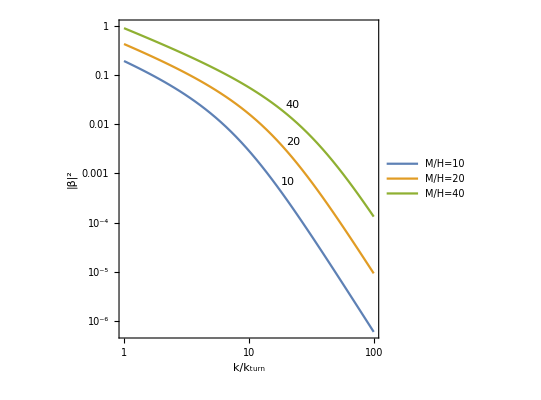

```mathematica
(* liczba obsadzeń w uproszczonej wersji *)
Block[{ml={Subscript[m, ϕ]},mh={M}, kwT,kw, Nkw, r,lo,oznaczenia,legenda},(Nkw=3.;
ml={10^(-7),10^(-7),10^(-7)};mh={10^(-4),2*10^(-4),4*10^(-4)};

{kwT,kw}=Take[WektorFalowyTest[Nkw,pola,fG,La,g,x,fR,tloi,tf,fun,param,N0t],2];

r=MapThread[Sqrt[(kw^2+#2^2)/(kw^2+#1^2)] &,{ml,mh}];
Print["k_turn: ",SetPrecision[kwT,3]," ; k(N=",Nkw,")=",SetPrecision[kw,3],": ",SetPrecision[(((Sqrt[r]-1/Sqrt[r])Sin[Δθ])^2)/4 /. param,3]];
lo=Function[{k,ml,mh},(((Sqrt[Sqrt[(k^2+mh^2)/(k^2+ml^2)]]-1/Sqrt[Sqrt[(k^2+mh^2)/(k^2+ml^2)]])Sin[Δθ])^2)/4 /. param];

oznaczenia={10,20,40};
legenda=Map["StyleBox[\"M\",\nFontSlant->\"Italic\"]/StyleBox[\"H\",\nFontSlant->\"Italic\"]="<>ToString[#] &,oznaczenia];
LogLogPlot[Evaluate[MapThread[Labeled[lo[k*kwT,ml[[#1]],mh[[#1]]],#2,{Scaled[0.5],Above}] &, {Range[Length[oznaczenia]],oznaczenia}]],{k,1,1*10^2},Frame->True, AspectRatio->1, FrameLabel->{"StyleBox[\"k\",\nFontSlant->\"Italic\"]/SubscriptBox[ StyleBox[\"k\",\nFontSlant->\"Italic\"], \"turn\"]","|β|^2"},PlotLegends->Placed[legenda,{Left,Bottom}]]
)]
```

```mathematica
(* gęstość energii wyprodukowanych ciężkich cząstek w uproszczonej wersji *)
Block[{mh},(mh={10^(-4), 2*10^(-4), 4*10^(-4), 5*10^(-4), 10^(-3),1.5*10^(-3),1.65*10^(-3),1.7*10^(-3),1.8*10^(-3),1.9*10^(-3), 2*10^(-3)};
Print["l ", N[mh^4*Sin[Δθ]^2/(24*Pi^2) /. param]];
Print["h ", N[mh^4*Sin[Δθ]^2/(16*Pi^2) /. param]];)]
```

l {4.03138×10^-20,6.45021×10^-19,1.03203×10^-17,2.51961×10^-17,4.03138×10^-16,2.04089×10^-15,2.98806×10^-15,3.36705×10^-15,4.23198×10^-15,5.25373×10^-15,6.45021×10^-15}

h {6.04707×10^-20,9.67531×10^-19,1.54805×10^-17,3.77942×10^-17,6.04707×10^-16,3.06133×10^-15,4.48209×10^-15,5.05057×10^-15,6.34797×10^-15,7.8806×10^-15,9.67531×10^-15}

```mathematica
(* wykresy elementów bazy wektorów własnych macierzy masy *)
WykresyBazaMasy[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];//AbsoluteTiming
```

19:11:40GMT+2.TimeObject[{19,11,40.1239},TimeZone→2.] Liczba e-powiększeń i baza wektorów własnych macierzy masy

19:11:40GMT+2.TimeObject[{19,11,40.1401},TimeZone→2.] Wykres wierszy 1

19:11:41GMT+2.TimeObject[{19,11,41.6062},TimeZone→2.] Wykres wierszy 2

19:11:41GMT+2.TimeObject[{19,11,41.9243},TimeZone→2.] Wykres kolumn 1

19:11:42GMT+2.TimeObject[{19,11,42.2258},TimeZone→2.] Wykres kolumn 2

{2.43994,Null}

```mathematica
(* wykresy elementów bazy Freneta *)
WykresyBaza[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];//AbsoluteTiming
```

04:24:12GMT+2.TimeObject[{4,24,12.9572},TimeZone→2.] Liczba e-powiększeń i baza

04:24:12GMT+2.TimeObject[{4,24,12.9602},TimeZone→2.] Wykres wierszy 1

04:24:13GMT+2.TimeObject[{4,24,13.6603},TimeZone→2.] Wykres wierszy 2

04:24:13GMT+2.TimeObject[{4,24,13.9778},TimeZone→2.] Wykres kolumn 1

04:24:14GMT+2.TimeObject[{4,24,14.3259},TimeZone→2.] Wykres kolumn 2

{1.72891,Null}

```mathematica
Test 
(* wykresy funkcji zależnych od pól i liczby e-powiększeń oraz ich pierwszych pochodnych w zależności od liczby e-powiększeń *)
Block[{funkcje,opisy,lista=Join[{{tf}},listaN1],
Lao,Xo,eps,mu,kk,tk000,Ebaza,Vsigsig,polat,mmm},(
(*funkcje={Map[#'[x[[1]]]/Symbol["nn"]'[x[[1]]] &, pola]};
opisy={{"wkladPM",Map[ToString[#]<>"'(t)/H" &, pola]}};*)

(*funkcje={Simplify[WspolczynnikiOddzialywaniaAE[pola,fG,La,g,x,fR,False]] // Flatten};
opisy={{"C","coefficients",{"C_σs1","C_s1σ"}}};*)

funkcje={{Symbol["nn"]'[x[[1]]]}};
opisy={{"H","H",{"H"}}};

Xo=Take[mrkLagrange`lagrangianO[g,x,pola,fG,La],{3}][[1]]/. Symbol["P"]->0;
funkcje={{Sqrt[2*Xo]}};
opisy={{"dsigma","dsigma",{"dsigma"}}};

eps=-Symbol["nn"]''[x[[1]]]/Symbol["nn"]'[x[[1]]]^2;
funkcje={{eps}};
opisy={{"eps","",{"ϵ"}}};

polat=Map[#[x[[1]]] &, pola];
funkcje={Map[#[x[[1]]] &, {pola[[2]]}]};
opisy={{"pola","",Map[ToString[#]<>"'(t)" &,{pola[[2]]}]}};

funkcje={{Symbol["nn"]''[x[[1]]]}};
opisy={{"dH","dH",{"dH"}}};

mu=Sqrt[9/4-(0/Symbol["nn"]'[x[[1]]])^2]/.param;
kk=0.001;tk000=578412.8;
(*kk=1.;tk000=pm0;*)
(*funkcje={{Abs[Exp[I Pi (mu + 1/2)/2]Sqrt[Pi]/2 Sqrt[Abs[kk * Symbol["τ"][x[[1]]]]]HankelH1[mu,Abs[kk * Symbol["τ"][x[[1]]]]]]/Exp[Symbol["nn"][x[[1]]]]}};*)
(*funkcje={{Abs[Exp[I Pi (mu + 1/2)/2]Sqrt[Pi]/2 Sqrt[kk * 3.2*10^10]HankelH1[mu,kk * 3.2*10^10]/Exp[Symbol["nn"][x[[1]]]]]^2}};
opisy={{"ua","u/a",{"u/a"}}};*)
funkcje={{Abs[(Symbol["nn"]'[x[[1]]]/Sqrt[2*Xo])Exp[I Pi (mu + 1/2)/2](Sqrt[Pi]/2 )Sqrt[Abs[Symbol["τ"][x[[1]]]]]HankelH1[mu,kk * Abs[Symbol["τ"][x[[1]]]]]/Exp[Symbol["nn"][x[[1]]]]]^2}};
opisy={{"Rua","Ru/a",{"Ru/a"}}};
funkcje={{((Symbol["nn"]'[x[[1]]]/(Exp[Symbol["nn"][x[[1]]]]*Sqrt[2*Xo]))^2/.x[[1]]->tk000)(1+1/(kk*Symbol["τ"][x[[1]]])^2)/(2*kk)}};
opisy={{"Rua","Ru/a",{"Ru/a"}}};
funkcje={{kk^3/(2*Pi^2)*Abs[((Symbol["nn"]'[x[[1]]]/Sqrt[2*Xo])/.x[[1]]->tk000)Exp[I Pi (mu + 1/2)/2](Sqrt[Pi]/2 )Sqrt[Abs[Symbol["τ"][x[[1]]]]]HankelH1[mu,kk * Abs[Symbol["τ"][x[[1]]]]]/Exp[Symbol["nn"][x[[1]]]]]^2}};
opisy={{"PRua","PRu/a",{"PRu/a"}}};

Ebaza=BazaFreneta[g,x,pola,fG,La];
Vsigsig=Sum[Ebaza[[1,I]]Ebaza[[1,J]]D[D[V[Sequence@@polat]/.fun,polat[[I]]],polat[[J]]],{I,1,lpol},{J,1,lpol}];
funkcje={{((Symbol["nn"]'[x[[1]]]^2/(2*Pi*Sqrt[2*Xo]))^2/.x[[1]]->tk000)*(1+kk^2*Symbol["τ"][x[[1]]]^2)*(1-2*(eps/.x[[1]]->tk000)+(2*(3*eps-Vsigsig/(3*Symbol["nn"]'[x[[1]]]^2))/.x[[1]]->tk000)*Re[(D[HankelH1[mmm,kk * Abs[Symbol["τ"][x[[1]]]] /(1+(eps/.x[[1]]->tk000))],mmm]/.mmm->mu)/HankelH1[mu,kk * Abs[Symbol["τ"][x[[1]]]] /(1+(eps/.x[[1]]->tk000))]])}};
opisy={{"PRsr_k1","PRsr",{"PRsr"}}};
funkcje={{(1+kk^2*Symbol["τ"][x[[1]]]^2)*(1-2*(eps/.x[[1]]->tk000)+(2*(3*eps-Vsigsig/(3*Symbol["nn"]'[x[[1]]]^2))/.x[[1]]->tk000)*Re[(D[HankelH1[mmm,kk * Abs[Symbol["τ"][x[[1]]]] /(1+(eps/.x[[1]]->tk000))],mmm]/.mmm->mu)/HankelH1[mu,kk * Abs[Symbol["τ"][x[[1]]]] /(1+(eps/.x[[1]]->tk000))]])}};
opisy={{"PRsrn_k0,001","PRsrn",{"PRsrn"}}};

(*funkcje={{Symbol["nn"]'[x[[1]]]Exp[Symbol["nn"][x[[1]]]]}};
opisy={{"da","da",{"da"}}};*)

(*Lao=Take[mrkLagrange`lagrangianO[g,x,pola,fG,La],{4}][[1]]/. Symbol["P"]->0;*)

(*funkcje={{Abs[Symbol["τ"][x[[1]]]]}};
opisy={{"tau","tau",{"tau"}}};*)

funkcje={{kk^3*Symbol["τ"][x[[1]]]^3}};
opisy={{"ktau3","ktau3",{"ktau3"}}};

WykresyTestoweTlo[funkcje,opisy,pola,fG,La,g,x,fR,tloi,lista,fun,param,sciezka,N0t];)]//AbsoluteTiming
```

Test

3.23228482053665521362745×10^10

14:01:30GMT+1.TimeObject[{14,1,30.0878},TimeZone→1.] Liczba e-powiększeń

14:01:30GMT+1.TimeObject[{14,1,30.1034},TimeZone→1.] Wykres 1

14:01:55GMT+1.TimeObject[{14,1,55.6878},TimeZone→1.] Liczba e-powiększeń

14:02:05GMT+1.TimeObject[{14,2,5.23951},TimeZone→1.] Wykres 1

{59.3259,Null}

### Perturbacje

```mathematica
(* widma *)
(* widma w zależności od liczby e-powiększeń *)
Print[TimeObject[Now]];
Widma[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"N",3.},NkwNorm->3.,norm->"t",tftot->tfTot,baza->"F"];//AbsoluteTiming
```

$Aborted

```mathematica
(* perturbacje w zależności od liczby e-powiększeń *)
PerturbacjeB[pola,fG,La,g,x,fR,tloi,listaN1[[1]],fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"wsp",0.001},NkwNorm->0.,norm->"",tftot->tfTot,baza->"",RS->False,pertu->False];//AbsoluteTiming
```

{(H[t] (Qϕkw[t] ϕ'[t]+Qχkw[t] χ'[t]))/(ϕ'[t]^2+χ'[t]^2),-1/H[t]^2 H'[t] ((H'[t] (Qϕkw[t] ϕ'[t]+Qχkw[t] χ'[t]))/(ϕ'[t]^2+χ'[t]^2)+1/(√(ϕ'[t]^2+χ'[t]^2))H[t] ((Qϕkw'[t] ϕ'[t]+Qχkw'[t] χ'[t]+Qχkw[t] (-3 H[t] χ'[t]-V^(0,1)[ϕ[t],χ[t]])+Qϕkw[t] (-3 H[t] ϕ'[t]-V^(1,0)[ϕ[t],χ[t]]))/(√(ϕ'[t]^2+χ'[t]^2))-((Qϕkw[t] ϕ'[t]+Qχkw[t] χ'[t]) (2 χ'[t] (-3 H[t] χ'[t]-V^(0,1)[ϕ[t],χ[t]])+2 ϕ'[t] (-3 H[t] ϕ'[t]-V^(1,0)[ϕ[t],χ[t]])))/(2 (ϕ'[t]^2+χ'[t]^2)^(3/2)))-(H[t] (Qϕkw[t] ϕ'[t]+Qχkw[t] χ'[t]) (-3 H[t] (ϕ'[t]^2+χ'[t]^2)-χ'[t] V^(0,1)[ϕ[t],χ[t]]-ϕ'[t] V^(1,0)[ϕ[t],χ[t]]))/((ϕ'[t]^2+χ'[t]^2)^2))}

1.36557×10^7-2.42474×10^7 ⅈ {1.36557×10^7-2.42474×10^7 ⅈ,0.108541-0.192829 ⅈ}

02:14:01GMT+1.TimeObject[{2,14,1.17519},TimeZone→1.] Liczba e-powiększeń i widma

kw 9.99506×10^-9

tf A {7.00447×10^9,1.1094×10^9}

tf {Re,Im} {{{3.43707×10^9,674967.},{5.44379×10^8,106913.}},{{6.10321×10^9,1.19847×10^6},{9.66656×10^8,189835.}}}

02:14:01GMT+1.TimeObject[{2,14,1.80613},TimeZone→1.] Wykres perturbacji

02:14:45GMT+1.TimeObject[{2,14,45.2063},TimeZone→1.] Wykres wierszy 1

02:15:02GMT+1.TimeObject[{2,15,2.8091},TimeZone→1.] Wykres wierszy 2

02:15:11GMT+1.TimeObject[{2,15,11.3435},TimeZone→1.] Wykres kolumn 1

02:15:15GMT+1.TimeObject[{2,15,15.4403},TimeZone→1.] Wykres kolumn 2

02:15:23GMT+1.TimeObject[{2,15,23.4419},TimeZone→1.] Wykres Re

02:15:37GMT+1.TimeObject[{2,15,37.8898},TimeZone→1.] Wykres Im

{1193.04,Null}

```mathematica
(* widma w bazie wektorów własnych macierzy masy w zależności od liczby e-powiększeń *)
Print[TimeObject[Now]];
Block[{grid={},opisy={},zakres={},lista=listaExtra26[[12;;All]],listaNkw},
(*grid={{},{p01},{pm0,p01},{pm0,p005,p01},{m002,pm0,p005,p01},{m01,m002,pm0,p005,p01}};*)
opisy={"0.1","0.5","1"};
opisy={"1","2","10","20"};
opisy={};
listaNkw=Map[{"wsp",#} &, {0.1,0.5,1.}];
listaNkw=Map[{"wsp",#} &, {1.,2.,10.,20.}];
listaNkw=Map[{"wsp",#} &, Table[1.,Length[lista]]];
(*lista=Table[{tf},Length[listaNkw]];*)
(*zakres={Table[m1,Length[lista]],Join[{p2},Table[p2,Length[lista]-1]]};*)
(*zakres={Table[m1,Length[lista]],Join[{tf},Table[tf,Length[lista]-1]]};*)
zakres={Table[m01,Length[lista]],Join[{p02},Table[p02,Length[lista]-1]]};
WidmaB[pola,fG,La,g,x,fR,tloi,lista,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->listaNkw,NkwNorm->0.,norm->"h",tftot->tfTot,baza->"M",RS->True,pertu->False,zakrest->zakres,gridt->grid,legenda->opisy];]//AbsoluteTiming
```

00:15:58GMT+1.TimeObject[{0,15,58.1343},TimeZone→1.]

norm P* 3.91889×10^-8

kw {0.0000100006,0.0000100006,0.0000100006,0.0000100006,0.0000100006,0.0000100006}

tf {{6.93396×10^7,1138.66},{6.00685×10^7,1133.53},{4.50875×10^7,1315.16},{3.00603×10^7,1486.31},{2.4161×10^7,1574.51},{2.42237×10^7,2060.3}}

00:16:08GMT+1.TimeObject[{0,16,8.62011},TimeZone→1.] Wykres widm 1

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

Part::partw: Part 4 of If[Thickness[Large]==Dashing[{Small,Small}]&&Thickness[Large]==Dashing[{Small,Small}]&&Thickness[Large]==Dashing[{Small,Small}]&&Thickness[Large]==Dashing[{Small,Small}]&&Thickness[Large]==Dashing[{Small,Small}]&&Thickness[Large]==Dashing[{Small,Small}],mrkWykresy`Private`styl/.Dashed→Thick,mrkWykresy`Private`styl] does not exist.

Part::partw: Part 5 of If[Thickness[Large]==Dashing[{Small,Small}]&&Thickness[Large]==Dashing[{Small,Small}]&&Thickness[Large]==Dashing[{Small,Small}]&&Thickness[Large]==Dashing[{Small,Small}]&&Thickness[Large]==Dashing[{Small,Small}]&&Thickness[Large]==Dashing[{Small,Small}],mrkWykresy`Private`styl/.Dashed→Thick,mrkWykresy`Private`styl] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

05:12:02GMT+1.TimeObject[{5,12,2.13512},TimeZone→1.] Wykres widm 2

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of $IterationLimit::itlim will be suppressed during this calculation.

07:53:32GMT+1.TimeObject[{7,53,32.275},TimeZone→1.] Wykres widm

$Aborted

```mathematica
(* całość*)
"tf "{{0.9959690448860465,1.105174509358281*^-8},{1.0863753554692402*^9,0.7431048755402431}}
(* tylko zeta *)
"tf "{{0.9959690448860465,1.105174509358281*^-8},{18461.42024297196,0.00003830526553988774}}

"19:15:06""GMT+"1.TimeObject[{19,15,6.3838366},TimeZone->1.]
-1112.7659459571794+2576.2576793839635 ⅈ" "{0.014279136782312818-0.0218125930274195 ⅈ,-1112.7659459571794+2576.2576793839635 ⅈ}
"kw "{0.00009995060204903567,0.00009995060204903567}
"tf "{{1.104239475841654,0.000019903744446531962},{9.713178450299997*^6,34.80054952372176}}
```

```mathematica
"tf "{{0.9959690448860467,1.105174509358281*^-8},{1.5853798801204777,9.689003743801292*^-9},{4.41078529728955,8.183876501954764*^-9},{7.4844134388293275,8.169568498516305*^-9},{7.585448441690447,8.181082387674379*^-9}}
```

```mathematica
"tf "{{0.9959690448860467,1.105174509358281*^-8},{1.5039547091531733,7.737832363637492*^-9},{0.6740757907133594,6.8579450877840015*^-9},{0.01676997705247868,5.567589662885958*^-9},{0.04995231755328291,5.880966230186277*^-9}}
```

```mathematica
(* widma w bazie Freneta w zależności od liczby falowej *)
Print[TimeObject[Now]];
Widma[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"",0.},NkwNorm->0.,norm->"h",tftot->tfTot,baza->"F"];//AbsoluteTiming
```

$Aborted

```mathematica
(* widma w bazie wektorów własnych macierzy masy w zależności od liczby falowej *)
Print[TimeObject[Now]];
WidmaB[pola,fG,La,g,x,fR,tloi,{{tf},listatfn1},fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"",0.},NkwNorm->0.,norm->"h",tftot->tfTot,baza->"M",RS->True,pertu->False,zakrest->{{0.,0.},{tf,tf}}];//AbsoluteTiming
```

```mathematica
(* wzmocnienia widma perturbacji krzywizny w zależności od liczby falowej *)
Print[TimeObject[Now]];
Block[{punkty,listaNkwNorm,opisy={},lista={listaExtra26[[9]]}},
punkty=Map[{"wsp", #} &, Join[Range[0.1,1.6,0.2],Range[1.6,10.,1.]]];
punkty=Map[{"wsp", #} &, {0.001,0.005,0.01,0.05,0.1,0.5,1.,1.5,2.,2.5,3.,3.5}];
punkty=Map[{"wsp", #} &, {0.001,0.005,0.01,0.05,0.1,0.5,1.}];
(*punkty=Map[{"wsp", #} &, {0.3, 0.6, 1., 2., 5., 10.}];*)
(*punkty=Map[{"wsp", #} &, {0.1, 0.5, 1., 2., 5., 10.}];*)
(*punkty=Map[{"wsp", #} &, {0.1,0.3,0.5,0.7,1.,2.,2.5,3.,4.,5.,6.,7.,8.,9.,10.}];
punkty=Map[{"wsp", #} &, {0.1,1.,2.,10.}];*)
listaNkwNorm=Table[0.,Length[lista]];
opisy=listaExtra1500Nazwy;
opisy={listaExtra1500Nazwy[[1]],listaExtra1500Nazwy[[3]],listaExtra1500Nazwy[[5]]};
opisy={listaExtra26Nazwy[[9]]};
WzmocnienieB[pola,fG,La,g,x,fR,tloi,lista,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->punkty, NkwNorm->listaNkwNorm,baza->"M",nrwidm->{1},legenda->opisy]]//AbsoluteTiming
```

16:19:28GMT+2.TimeObject[{16,19,28.8888},TimeZone→2.]

16:19:28GMT+2.TimeObject[{16,19,28.9669},TimeZone→2.]Rozwiązanie 1

16:19:28GMT+2.TimeObject[{16,19,28.9669},TimeZone→2.] Równanie pola 00 w rzędzie 0

16:19:29GMT+2.TimeObject[{16,19,29.1628},TimeZone→2.] Równania ruchu w rzędzie 0

16:19:30GMT+2.TimeObject[{16,19,30.0424},TimeZone→2.] Równania ruchu w rzędzie 0

16:19:34GMT+2.TimeObject[{16,19,34.6253},TimeZone→2.] Równania ruchu w rzędzie 1

16:19:34GMT+2.TimeObject[{16,19,34.6722},TimeZone→2.] Równania ruchu w rzędzie 1

16:19:34GMT+2.TimeObject[{16,19,34.8441},TimeZone→2.] Równanie pola 11 w rzędzie 0

16:19:34GMT+2.TimeObject[{16,19,34.8992},TimeZone→2.] Równanie pola 00 w rzędzie 1

16:19:35GMT+2.TimeObject[{16,19,35.0555},TimeZone→2.] Równanie pola 01 w rzędzie 1

16:19:35GMT+2.TimeObject[{16,19,35.1486},TimeZone→2.] Równania ruchu dla zmiennych Mukhanova-Sasakiego

16:19:35GMT+2.TimeObject[{16,19,35.9648},TimeZone→2.] Baza Freneta

16:19:36GMT+2.TimeObject[{16,19,36.4958},TimeZone→2.] Rozwiązania z produkcją cząstek

16:26:07GMT+2.TimeObject[{16,26,7.76282},TimeZone→2.]500

16:34:57GMT+2.TimeObject[{16,34,57.5247},TimeZone→2.]1000

16:41:29GMT+2.TimeObject[{16,41,29.6274},TimeZone→2.]1500

17:40:59GMT+2.TimeObject[{17,40,59.8294},TimeZone→2.]2000

17:47:39GMT+2.TimeObject[{17,47,39.2234},TimeZone→2.]2500

{ttot, gtot, gtot/a3} {-0.313655,{2.03789×10^-15,3.05683×10^-15},{1.96923×10^-15,1.3692×10^-16}}

19:38:42GMT+2.TimeObject[{19,38,42.6481},TimeZone→2.] Wykres widm(k) - wzmocnienia(k)

{11955.1,Null}

```mathematica
(* punkty=Map[{"wsp", #} &, {0.1,0.3,0.5,0.7,1.,2.,2.5,3.,4.,5.,6.,7.,8.,9.,10.}];
{{tf},listatfn2} *)
{{{0.1,0.9876171190824801},{0.29999999999999993,0.9906318317909778},{0.49999999999999994,1.0016546386896203},{0.6999999999999998,1.0231606669962032},{0.9999999999999999,1.0785430406702896},{1.9999999999999998,1.351131254162129},{2.4999999999999996,1.3966253448609658},{2.9999999999999996,1.3233419976986953},{3.9999999999999996,1.0452929844786882},{4.999999999999999,1.0373814461629576},{5.999999999999999,1.1431897297602687},{7.,1.0564101922980118},{7.999999999999999,1.014035296059254},{8.999999999999998,1.088681236872553},{9.999999999999998,1.0632092895879846}},{{0.1,15.359009033832272},{0.29999999999999993,16.08499229052795},{0.49999999999999994,17.427384209369833},{0.6999999999999998,19.17225868314315},{0.9999999999999999,21.91386132934547},{1.9999999999999998,21.181668163017886},{2.4999999999999996,13.195742276742862},{2.9999999999999996,4.5541499934730245},{3.9999999999999996,1.980341324772158},{4.999999999999999,13.000798306480407},{5.999999999999999,9.753949071942234},{7.,0.5108120350187195},{7.999999999999999,3.5905831293304726},{8.999999999999998,6.168858694727985},{9.999999999999998,1.2903312692047897}}}


(* Pk - 0 *)
{{{0.1,0.9876171190824801},{0.2,0.9885028462134687},{0.3,0.9906318322583718},{0.4,0.9950238043594833},{0.49999999999999994,1.0016546386896203},{0.5999999999999999,1.0109637727047942},{0.7000000000000001,1.0231606095454926},{0.8,1.0383438183769655},{0.8999999999999999,1.057186190275632},{0.9999999999999999,1.0785430406702896},{1.1,1.1027721937432977},{1.2,1.1298077102994348},{1.3,1.1582848201251148},{1.4000000000000001,1.187507327908387},{1.5,1.2177555849710304},{1.6,1.2473171222708808},{1.7,1.276438279380155},{1.8000000000000003,1.304292154673044},{1.9,1.3286676841648801},{1.9999999999999998,1.351131254162129},{2.0999999999999996,1.3690254638880086},{2.2,1.3828569508423834},{2.3,1.3923316939712855},{2.4,1.3971068359472878},{2.5000000000000004,1.3966253434625522},{2.6,1.390716675794293},{2.6999999999999997,1.380723846331224},{2.8000000000000003,1.3653476241455602},{2.9,1.346431032969762},{3.,1.3233419976986953},{3.1,1.297166765898299},{3.2,1.2687833699587407},{3.3,1.2387390910042653},{3.4,1.2077649024275219},{3.5,1.1766753099656495},{3.5999999999999996,1.146262040725412},{3.6999999999999997,1.117269553125542},{3.8,1.0903882640202898},{3.8999999999999995,1.0662322720360065},{3.9999999999999996,1.0452929844786882},{4.1,1.027927037629423},{4.199999999999999,1.0144101911307566},{4.3,1.004910876944129},{4.399999999999999,0.9994291739354728},{4.499999999999999,0.9978600074872325},{4.6,0.9999774847278996},{4.7,1.005451221778378},{4.799999999999999,1.0138517021433193},{4.8999999999999995,1.024683290702745},{4.999999999999999,1.0373814461629576},{5.099999999999999,1.051346160735774},{5.2,1.0659885144148704},{5.299999999999999,1.080646338427171},{5.3999999999999995,1.0948096269204237},{5.5,1.1078830834408286},{5.599999999999999,1.1193794419316774},{5.699999999999999,1.1289633149455565},{5.8,1.1362614211247632},{5.8999999999999995,1.1410264137061967},{5.999999999999999,1.1431897297602687},{6.1,1.1427308168512302},{6.2,1.1396829902225354},{6.299999999999999,1.1342043562136075},{6.4,1.1265653275441438},{6.499999999999999,1.1170970119128933},{6.599999999999999,1.1061693135198227},{6.699999999999999,1.0941907285897057},{6.8,1.0816022158629675},{6.8999999999999995,1.0688591586253688},{7.,1.0564101922980118},{7.099999999999999,1.0446787395971058},{7.199999999999999,1.0340483235808602},{7.299999999999999,1.024850635526138},{7.3999999999999995,1.017355481996348},{7.499999999999999,1.0117630195169545},{7.6,1.0081983769403065},{7.7,1.0067091656433151},{7.799999999999999,1.0072658647387487},{7.9,1.009765048341474},{7.999999999999999,1.014035296059254},{8.099999999999998,1.019845417537366},{8.2,1.0269147206259956},{8.299999999999999,1.0349247776826944},{8.399999999999999,1.0435323080425725},{8.5,1.0523825469693413},{8.6,1.0611226599638357},{8.699999999999998,1.0694144860838317},{8.8,1.0769464984180503},{8.9,1.0834445329367217},{8.999999999999998,1.088681236872553},{9.1,1.09248402748953},{9.2,1.0947408678992525},{9.299999999999999,1.0954029123018107},{9.4,1.094483577832338},{9.5,1.0920545507791526},{9.599999999999998,1.0882406907160498},{9.700000000000001,1.083215430122762},{9.799999999999999,1.0771959663674615},{9.899999999999999,1.0704352603265845},{9.999999999999998,1.0632092895879846}}}


(* Pk - 0, 382 M150*)
{{{0.1,0.9959690448860462},{0.2,0.9979780999366079},{0.30000000000000004,1.0028761784082778},{0.4,1.0115743493819258},{0.5,1.0253408943364732},{0.6,1.044513400321288},{0.7000000000000001,1.0694690244702176},{0.8,1.101058125772909},{0.9,1.1387571320000442},{1.,1.1822018425559888},{1.1,1.231606611944922},{1.2000000000000002,1.284798156703799},{1.3000000000000003,1.3417653420298983},{1.4000000000000001,1.4003875776945856},{1.5000000000000002,1.4606655000921218},{1.6,1.519518645046419},{1.7000000000000002,1.5767360031971729},{1.8000000000000005,1.6307366457701142},{1.9000000000000001,1.679724355823614},{2.,1.7212668696532667},{2.1,1.7566724701888659},{2.2,1.782152275902169},{2.3000000000000003,1.799099344345499},{2.4000000000000004,1.806320355819543},{2.5000000000000004,1.8031188412931574},{2.6,1.789730099982391},{2.7,1.7665563334564351},{2.8000000000000003,1.7341293456578961},{2.9000000000000004,1.693215329421703},{3.0000000000000004,1.6450058812029176},{3.1000000000000005,1.5910376260645773},{3.2,1.5324506707504606},{3.3000000000000003,1.4704344223600556},{3.4000000000000004,1.4072006433368596},{3.5,1.3439483561901182},{3.6,1.282359849583041},{3.7,1.2239504326380963},{3.8000000000000003,1.1700325287835487},{3.9,1.1217797179115419},{4.,1.080251668188302},{4.1,1.0461067560216395},{4.2,1.0199233100814311},{4.3,1.001932679877033},{4.3999999999999995,0.9921197976400604},{4.5,0.9902314402924637},{4.6,0.9957698576358853},{4.7,1.0080223800779047},{4.8,1.026088880929806},{4.9,1.0489208405311858},{5.,1.075361965657902},{5.1,1.104184486045754},{5.2,1.1341292423835108},{5.3,1.1639507561192817},{5.4,1.1924615017851294},{5.5,1.2185712526804415},{5.6,1.2413204594140284},{5.7,1.2599081132236358},{5.8,1.2737135729486533},{5.9,1.2823120903174856},{6.,1.2854831545942516},{6.1,1.2832115992047899},{6.200000000000001,1.2756815778265753},{6.299999999999999,1.2632637206471742},{6.4,1.2464964492295518},{6.500000000000001,1.226061908545652},{6.599999999999999,1.2027573316197568},{6.7,1.1774625349243533},{6.800000000000001,1.1511043523432947},{6.9,1.1246200244075737},{7.,1.0989221488403096},{7.1000000000000005,1.0748675749306429},{7.2,1.053230605015756},{7.300000000000001,1.0346785068464353},{7.4,1.019747960989728},{7.5,1.0088255913590052},{7.6000000000000005,1.002137773345943},{7.7,0.9997500902213281},{7.8,1.0015704935819412},{7.9,1.0073539452731257},{8.,1.0167150683765052},{8.1,1.0291502233774652},{8.2,1.0440581203266583},{8.3,1.0607582797089694},{8.4,1.0785230904625676},{8.5,1.0966160986501317},{8.6,1.1143085791206426},{8.7,1.1308936312955862},{8.8,1.1457335824327788},{8.9,1.1582930324923024},{9.,1.1681212697530674},{9.1,1.1748683742484762},{9.2,1.1783398888859764},{9.3,1.1784736008478491},{9.4,1.1753030610608697},{9.5,1.1690072733338148},{9.6,1.1599006029578438},{9.700000000000001,1.148362146750703},{9.8,1.1348638113047718},{9.9,1.119965794514969},{10.,1.1042394758416543}},{{0.1,7.070268871730846},{0.2,7.176041446387899},{0.30000000000000004,7.349814293319774},{0.4,7.585748541369419},{0.5,7.876099024704283},{0.6,8.210630481072354},{0.7000000000000001,8.577646319721353},{0.8,8.964433741478027},{0.9,9.35645421439698},{1.,9.739222507471977},{1.1,10.098558958242206},{1.2000000000000002,10.419193186309329},{1.3000000000000003,10.68854390472974},{1.4000000000000001,10.893899942313201},{1.5000000000000002,11.025544519619254},{1.6,11.074183897987174},{1.7000000000000002,11.034451648234459},{1.8000000000000005,10.902589132323769},{1.9000000000000001,10.677334330937645},{2.,10.359391972987376},{2.1,9.954487806461213},{2.2,9.467369498801615},{2.3000000000000003,8.908243258690556},{2.4000000000000004,8.287288994589687},{2.5000000000000004,7.616620377976555},{2.6,6.910002269443695},{2.7,6.181944831850602},{2.8000000000000003,5.447271283226459},{2.9000000000000004,4.720750373264094},{3.0000000000000004,4.016804140038406},{3.1000000000000005,3.3490974398055613},{3.2,2.729692931172391},{3.3000000000000003,2.1689435508021915},{3.4000000000000004,1.6759766976525805},{3.5,1.2572131759063527},{3.6,0.9170849785658785},{3.7,0.6577450057464971},{3.8000000000000003,0.4789238886339317},{3.9,0.3781885153188272},{4.,0.35103786189836983},{4.1,0.3909972698164317},{4.2,0.4900696950244024},{4.3,0.6388839084381503},{4.3999999999999995,0.827102809208575},{4.5,1.0437817240402796},{4.6,1.2777277043879003},{4.7,1.517871161527677},{4.8,1.7536176706498539},{4.9,1.9751769499555873},{5.,2.1738517919133447},{5.1,2.342277101261375},{5.2,2.4746086470921465},{5.3,2.5666572431377297},{5.4,2.6159622221113117},{5.5,2.6218019082273893},{5.6,2.5851427813473706},{5.7,2.5085320166497493},{5.8,2.3959387296215833},{5.9,2.2525511861175196},{6.,2.084537927916947},{6.1,1.8987822579362246},{6.200000000000001,1.7026004203736629},{6.299999999999999,1.5034537155700343},{6.4,1.3086652935064187},{6.500000000000001,1.1251514356492454},{6.599999999999999,0.959176392985851},{6.7,0.8161387603481635},{6.800000000000001,0.7003958330683294},{6.9,0.6151315884449705},{7.,0.562272777633523},{7.1000000000000005,0.5424556502820521},{7.2,0.5550428946698915},{7.300000000000001,0.5981869242527349},{7.4,0.6689343479886105},{7.5,0.7633679375880165},{7.6000000000000005,0.8767829661993579},{7.7,1.0038908351562588},{7.8,1.1390379000173452},{7.9,1.2764293102220188},{8.,1.410353911917481},{8.1,1.535403564623071},{8.2,1.6466718873200756},{8.3,1.7399245896624156},{8.4,1.8117473493692957},{8.5,1.8596638615156906},{8.6,1.8822010103836413},{8.7,1.8789103121483552},{8.8,1.850373372947901},{8.9,1.798164442566176},{9.,1.72474276377337},{9.1,1.6333333909915708},{9.2,1.52781457680755},{9.3,1.4125383414208892},{9.4,1.2921235011914811},{9.5,1.1713030827267},{9.6,1.054742563945884},{9.700000000000001,0.946821516127303},{9.8,0.8514941692922372},{9.9,0.7721582597586125},{10.,0.7114983891767995}}}
```

```mathematica
Test 
(* widma dla podanej bazy *)
Print[TimeObject[Now]];
Block[{baza},(
baza={};
baza={{1,0,0},{0,1,0},{0,0,1}};
WidmaTest[baza,pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p];)]//AbsoluteTiming
```

16:15:53GMT+2.TimeObject[{16,15,53.1763},TimeZone→2.]

16:15:53GMT+2.TimeObject[{16,15,53.1919},TimeZone→2.] Perturbacje ℛ i 𝒮

16:15:54GMT+2.TimeObject[{16,15,54.8795},TimeZone→2.] Widma

16:15:55GMT+2.TimeObject[{16,15,55.0357},TimeZone→2.] Liczba e-powiększeń i widma

16:15:55GMT+2.TimeObject[{16,15,55.2857},TimeZone→2.] Wykres

{4.00844,Null}

```mathematica
(* korelacje względne *)
Print[TimeObject[Now]];
KorelacjeWzgledne[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->True,Nkw->{"N",3.}];//AbsoluteTiming
```

01:39:30GMT+2.TimeObject[{1,39,30.8356},TimeZone→2.]

01:39:30GMT+2.TimeObject[{1,39,30.8396},TimeZone→2.] Widma

01:39:30GMT+2.TimeObject[{1,39,30.8714},TimeZone→2.] Korelacje

01:39:30GMT+2.TimeObject[{1,39,30.8724},TimeZone→2.] Korelacje względne

01:39:30GMT+2.TimeObject[{1,39,30.8764},TimeZone→2.] Liczba e-powiększeń i względne korelacje

01:39:30GMT+2.TimeObject[{1,39,30.8784},TimeZone→2.] Wykres

{1.98064,Null}

```mathematica
Print[TimeObject[Now]];
Korelacje[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t,N0P->N0p,MS->mMS,Nkw->{"N",3.},NkwNorm->3.,norm->"h",tftot->tfTot];//AbsoluteTiming
```

01:40:34GMT+2.TimeObject[{1,40,34.8096},TimeZone→2.]

01:40:34GMT+2.TimeObject[{1,40,34.8252},TimeZone→2.] Korelacje

01:40:34GMT+2.TimeObject[{1,40,34.8428},TimeZone→2.] Liczba e-powiększeń i korelacje

01:40:34GMT+2.TimeObject[{1,40,34.8443},TimeZone→2.] Wykres

{1.56311,Null}

```mathematica
Test
(* liczby falowe dla N=0 (k1) i N=Nkw (k2) w momencie przekraczania promienia Hubble'a: k=aH; {k1, k2, k1-k2, k2/k1} *)
Block[{Nkw},(Nkw=3.;
WektorFalowyTest[Nkw,pola,fG,La,g,x,fR,tloi,tf,fun,param,N0t])]
```

Test

{9.99506235933683244134×10^-6,0.000200736634607383730912,-0.000190741572248046898471,20.083580010870738543}

```mathematica
(* liczby obsadzeń *)
(* liczba obsadzeń w zależności od liczby e-powiększeń *)
Print[TimeObject[Now]];
LiczbaObsadzen[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"N",3.},NkwNorm->0.,zakrest->tzakresB];//AbsoluteTiming
```

09:11:23GMT+2.TimeObject[{9,11,23.5762},TimeZone→2.]

09:11:23GMT+2.TimeObject[{9,11,23.5919},TimeZone→2.] Liczba e-powiększeń i liczba obsadzeń

{3.71329×10^-9,2.60026×10^-6}09:11:23GMT+2.TimeObject[{9,11,23.6075},TimeZone→2.]

{1.95593×10^-6,1.95594×10^-6}09:11:23GMT+2.TimeObject[{9,11,23.6387},TimeZone→2.]

{0.012178,0.0125118}09:11:23GMT+2.TimeObject[{9,11,23.67},TimeZone→2.]

09:11:23GMT+2.TimeObject[{9,11,23.67},TimeZone→2.] Wykres

{12.272,Null}

```mathematica
(* liczba obsadzeń w zależności od liczby falowej *)
Print[TimeObject[Now]];
LiczbaObsadzen[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"",0.},NkwNorm->0.,zakrest->{tB}];//AbsoluteTiming
```

03:26:01GMT+2.TimeObject[{3,26,1.53742},TimeZone→2.]

03:26:01GMT+2.TimeObject[{3,26,1.67498},TimeZone→2.] Liczba obsadzeń

kwNorm: {0.463267,0.829206}03:26:03GMT+2.TimeObject[{3,26,3.71264},TimeZone→2.]

1.5: {1.02366,0.375015}03:26:05GMT+2.TimeObject[{3,26,5.92366},TimeZone→2.]

2: {0.365702,0.228618}03:26:08GMT+2.TimeObject[{3,26,8.31438},TimeZone→2.]

10: {0.0139638,0.0138118}03:26:14GMT+2.TimeObject[{3,26,14.0065},TimeZone→2.]

20: {0.00205275,0.00223467}03:26:23GMT+2.TimeObject[{3,26,23.8839},TimeZone→2.]

03:26:23GMT+2.TimeObject[{3,26,23.8844},TimeZone→2.] Wykres

$Aborted

```mathematica
Test
(* gęstość energii wyprodukowanych na zakręcie cząstek w chwili t0 *)
Print[TimeObject[Now]];
GestoscEnergiiCzastekTest[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS, t0->tN0]//AbsoluteTiming
```

Test

04:56:04GMT+2.TimeObject[{4,56,4.98974},TimeZone→2.]

04:56:13GMT+2.TimeObject[{4,56,13.7468},TimeZone→2.] Gęstości energii wyprodukowanych cząstek

{{0.000099552,0},{0,0.00098715}}

{9.9951×10^-6,{0.00010005,0.0009872}}

4.45893×10^-14

8.78729×10^-14

$Aborted

```mathematica
(* indeks spektralny n_s dla perturbacji krzywizny i izokrzywizny: {kw,kw2,kw-kw2,indeks} *)
Print[TimeObject[Now]];
IndeksSpektralny[pola,fG,La,g,x,fR,tloi,tf,fun,param,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"N",0.},Nkw2->{"N",0.1},baza->"F"]//AbsoluteTiming
```

21:46:59GMT+2.TimeObject[{21,46,59.5367},TimeZone→2.]

21:49:56GMT+2.TimeObject[{21,49,56.8938},TimeZone→2.] Perturbacje ℛ i 𝒮

21:49:56GMT+2.TimeObject[{21,49,56.8947},TimeZone→2.] Widma

21:52:59GMT+2.TimeObject[{21,52,59.5428},TimeZone→2.] Perturbacje ℛ i 𝒮

21:52:59GMT+2.TimeObject[{21,52,59.5438},TimeZone→2.] Widma

{360.021,{9.9950602027799551257×10^-6,0.000011046213787470111263,-1.05115358469015614×10^-6,{1.22609,4.50165}}}

```mathematica
(* indeks spektralny n_s dla perturbacji krzywizny i izokrzywizny: {kw,kw2,kw-kw2,indeks} *)
Print[TimeObject[Now]];
IndeksSpektralnyB[pola,fG,La,g,x,fR,tloi,{tf},fun,param,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"N",0.},Nkw2->{"N",0.1},baza->"M"]//AbsoluteTiming
```

21:53:24GMT+2.TimeObject[{21,53,24.0279},TimeZone→2.]

Macierz masy: {{9.79×10^-8,-6.18×10^-7},{-6.18×10^-7,3.9×10^-6}}

Wartości własne macierzy masy: {-9.75×10^-15,4.×10^-6}

21:53:24GMT+2.TimeObject[{21,53,24.0569},TimeZone→2.] Perturbacje ℛ i 𝒮

21:53:24GMT+2.TimeObject[{21,53,24.0579},TimeZone→2.] Perturbacje ℛ i 𝒮

21:53:24GMT+2.TimeObject[{21,53,24.0589},TimeZone→2.] Widma

21:53:24GMT+2.TimeObject[{21,53,24.0599},TimeZone→2.] Widma

{0.0434116,{9.9950602027799551257×10^-6,0.000011046213787470111263,-1.05115358469015614×10^-6,{1.22767,3.0629}}}

```mathematica
{100.49275074522964,{9.9950602027799551257198695921235`20.44235095963348*^-6,0.00001104621378747011126339341470182748`20.023709035184876,-1.05115358469015613767354510970398`18.87341102014017*^-6,{1.2276740497668468,4.49553237582186}}} (*F*)
```

```mathematica
(* indeksy spektralne dla perturbacji oraz wzmocnienie perturbacji krzywizny *)
Block[{Nk=0.1,k1,k2,dk,indeksns,PRf,opisy,wartosci,nazwaplikuwp},(
(* liczby falowe i indeksy spektralne *)
{k1,k2,dk,indeksns}=IndeksSpektralnyB[pola,fG,La,g,x,fR,tloi,{tf},fun,param,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"N",0.},Nkw2->{"N",Nk},baza->"F"];
(* wzmocnienie perturbacji krzywizny *)
PRf=Wzmocnienie[pola,fG,La,g,x,fR,tloi,tf,fun,param,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"N",0.}, NkwNorm->0.];
(* zapisanie wyników *)
opisy=Join[ Map[#[[1]] &, param], {Subscript[N,"0t"],Subscript[N,"0p"],Subscript[N,"tot"]}, Map[Subscript[#,0]&, pola], Map[Subscript[OverDot[#],0]&, pola], {Subscript[k,0],Subscript[k,Nk],Δ k}, {Subscript[n,"s"](Subscript[P,ℛ])},Map[Subscript[n,"s"](Subscript[P,Subscript[𝒮,#]]) &, Range[lpol-1]], {λ}];
(*wartosci=Flatten[{Map[NumberForm[Round[#[[2]],0.01],NumberPoint->","] &, param], {N0t,N0p},Map[NumberForm[Round[#,0.001],NumberPoint->","] &, Flatten[{Ntot,tloi,k1,k2,dk,indeksns,PRf}]]}];*)
wartosci=Flatten[{Map[ScientificForm[If[Element[#[[2]],Rationals],N[#[[2]]],#[[2]]], 2, NumberMultiplier->"*",NumberPoint->","] &, param], {NumberForm[N0t,NumberPoint->","],NumberForm[N0p,NumberPoint->","]},Map[ScientificForm[If[Element[#,Rationals],N[#],#], 3, NumberMultiplier->"*",NumberPoint->","] &, Flatten[{Ntot,tloi,k1,k2,dk,indeksns,PRf}]]}];
(* nazwa tworzonego pliku z wartościami początkowymi i indeksem spektralnym *)
nazwaplikuwp=nazwaplikurow<>"_dane.txt";
PlikTexTabela[opisy,wartosci,nazwaplikuwp,sciezka];)]//AbsoluteTiming
```

{0.0324733,Null}

```mathematica
Quit[]
```